```mathematica
PltFmt=NotebookOpen["/Users/rileyhanus/Documents/Mathematica/Plot Formatting.nb",Visible->False];
SelectionMove[PltFmt,All,Notebook];
SelectionEvaluate[PltFmt];

Csts=NotebookOpen["/Users/rileyhanus/Documents/Mathematica/Constants.nb",Visible->False];
SelectionMove[Csts,All,Notebook];
SelectionEvaluate[Csts];
```

```mathematica
ρ=2.329*10^3;
C11=16.564*10^10 (*N m^-2 @ 298 K *);
C12=6.394*10^10;
C44=7.951*10^10;
```

```mathematica
(*Input: ϕ (rad) angle between direction and x̂ rotating around ŷ; Output: Subscript[v, S]^-1 (s/m);
q=vs^-1*)
qShear[ϕ_]:= (2 ρ)^(1/2)(C11+C44-((C11-C44)^2 Cos[2 ϕ]^2+(C12+C44)^2 Sin[2ϕ]^2)^(1/2))^(-1/2);
qLong[ϕ_]:=(2 ρ)^(1/2)(C11+C44+((C11-C44)^2 Cos[2 ϕ]^2+(C12+C44)^2 Sin[2ϕ]^2)^(1/2))^(-1/2);
SpeedArray[dϕ_,q_]:=Table[{q[ϕ]^-1 Cos[ϕ],q[ϕ]^-1 Sin[ϕ]},{ϕ,0,2π,dϕ}]
```

```mathematica
qLong[π/4]^-1
```

9133.8

Longitudinal speed in different crystal directions

```mathematica
vL100=(C11/ρ)^(1/2)
vL110=((C11+C12+2C44)/(2ρ))^(1/2)
vL111=((C11+2C12+4C44)/(3ρ))^(1/2)
"max Δv_s/v_s long"
(vL111-vL100)/((vL100+vL110+vL111)/3)
```

8433.31

9133.8

9355.65

max Δv_s/v_s

0.102777

Transverse speeds of sound in different crystal directions (and polarizations)

```mathematica
vT100=(C44/ρ)^(1/2) (*same as vT110 polarized in the [001] direction*)
vT110=((C11-C12)/(2ρ))^(1/2) 
vT111=((C11+C44-C12)/(3ρ))^(1/2)
"max Δv_s/v_s trans"
(vT100-vT110)/((vT100+vT110)/2)
```

5842.87

4672.62

5092.67

max Δv_s/v_s trans

0.222576

```mathematica
"max Δv_L/v_L"
(qLong[π/4]^-1-qLong[0]^-1)/((qLong[0]^-1+qLong[π/4]^-1)/2)
"max Δv_S/v_S"
(qShear[0]^-1-qShear[π/4]^-1)/((qShear[0]^-1+qShear[π/4]^-1)/2)
```

max Δv_L/v_L

0.079751

max Δv_S/v_S

0.222576

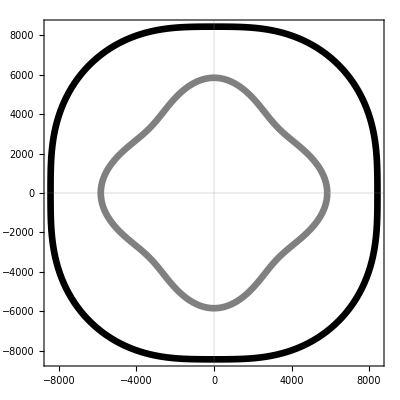

```mathematica
shadowbox[legend_]:=Graphics[{{White,EdgeForm[Black],Rectangle[]},Inset[legend,{0.5,0.5},Center]},AspectRatio->0.5,ImageSize->150]

ListPlot[{SpeedArray[π/100,qLong],SpeedArray[π/100,qShear]},
PlotStyle->{Directive[Black,Thickness[0.012]],Directive[Gray,Thickness[0.012]]},
FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times New Roman"],
PlotLegends->Placed[LineLegend[{Style["Longitudinal",18,FontFamily->"Times New Roman"],Style["Shear",18,FontFamily->"Times New Roman"]},
LegendFunction->shadowbox],{0.25,0.13}],
Joined->True,
AspectRatio->1,
GridLines->{{0},{0}}]
```